## Writing the data

### P_alfa-HDS

```mathematica
relativePath = "path";
subfolder = "folder/sub_folder/sub_sub_folder/";(*folder may be the name of the model; sub_folder may be 'more_a', 'equal' or 'more_b', based on the value of eps: in the first case, it should be +0.000001, in the second case it should be 0 and in the third case it should be -0.000001
sub_sub_folder may represent the value of z_a, e.g. za_0 or za_0_0_5. 
all these rules will be used when reading the filename*)
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Avm'[t] == Bvm[t]*(Avm[t]+Amr[t]+za)/tau[t]-Avm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t],
		Amr'[t]==  Bmr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]]-Amr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]],
		tau[t]==Avm[t]+Amr[t]+q*(Bvm[t]+Bmr[t])+za+zb,
		Bvm[t] == k-Avm[t],
		Bmr[t]==1-k-Amr[t],
		Avm[0]==(k)/2+eps,
		Amr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[relativePath<>subfolder<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[relativePath<>subfolder<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[relativePath<>subfolder<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[relativePath<>subfolder<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[relativePath<>subfolder<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k]

,{k,0,1,0.1}]
```

### Combinatorial-HDS

```mathematica
G=4;
path = "path/folder/sub_folder/sub_sub_folder/"; (*same rules as above*)
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
Do[
out = NDSolve[{Amr'[t]==Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Bmr[t]-Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Amr[t],
Avm'[t] == Bvm[t]*pa[t]-Avm[t]*pb[t],
		tau[t]==Amr[t]+Avm[t]+(Bmr[t]+Bvm[t])*q+za+zb,
		pa[t]==(za+Amr[t]+Avm[t])/tau[t],
		pb[t]==1-pa[t],
		Bvm[t]==k-Avm[t],
		Bmr[t]==1-k-Amr[t],
		Avm[0]==k*(0.5+eps),
		Amr[0]==(1-k)*(0.5+eps)
		}, 
	{Avm,Amr,Bvm,Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0.01,1,0.01}]
Export[path<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[path<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

### P_alfa-HCI

```mathematica
path = "path/folder/sub_folder/sub_sub_folder/"; (*same rules as above*);
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps =+0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Avm'[t] == Uvm[t]*(Avm[t]+Amr[t]+za)/tau[t]-Avm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t],
		Bvm'[t] == Uvm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t]-Bvm[t]*(Avm[t]+Amr[t]+za)/tau[t],
		Amr'[t] == Umr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]]-Amr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]],
		Bmr'[t] == Umr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]]-Bmr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]],
		tau[t]==Avm[t]+Amr[t]+q*(Bvm[t]+Bmr[t])+za+zb,
		Uvm[t] == k-Avm[t]-Bvm[t],
		Umr[t]==1-k-Amr[t]-Bmr[t],
		Avm[0]==k/2+eps,
		Bvm[0]==k/2-eps,
		Amr[0]==(1-k)/2+eps,
		Bmr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[path<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[path<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

### Combinatorial-HCI

```mathematica
relativePath = "path";
subfolder = "sub_folder/sub_sub_folder/"; (*same rules as above*)
G=4;
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimeSum=0.0;
convergenceTimes=List[];
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Amr'[t]==Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Umr[t]-Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Amr[t],
Bmr'[t]==-Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Bmr[t]+Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Umr[t],
Avm'[t] == Uvm[t]*pa[t]-Avm[t]*pb[t],
		Bvm'[t] == Uvm[t]*pb[t]-Bvm[t]*pa[t],
tau[t]==Amr[t]+Avm[t]+(Bmr[t]+Bvm[t])*q+za+zb,
		pa[t]==(za+Amr[t]+Avm[t])/tau[t],
		pb[t]==1-pa[t],
		Uvm[t] == k-Avm[t]-Bvm[t],
		Umr[t]==1-k-Amr[t]-Bmr[t],
		Avm[0]==k/2,
		Bvm[0]==k/2,
		Amr[0]==(1-k)/2+eps,
		Bmr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[relativePath<>subfolder<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[relativePath<>subfolder<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[relativePath<>subfolder<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[relativePath<>subfolder<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[relativePath<>subfolder<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

## Reading the data

### Plotting averaged accuracy, regret, convergence time and cognitive cost - direct switch

chds

za_0

{{{0.,3736/7575},{0.1,7451/15150},{0.2,1234/2525},{0.3,14651/30300},{0.4,4799/10100},{0.5,2337/5050},{0.6,1349/3030},{0.7,4243/10100},{0.8,1961/5050},{0.9,10529/30300},{1.,3029/10100}},{{0.,1146.82},{0.1,1156.88},{0.2,1178.6},{0.3,1214.33},{0.4,1271.71},{0.5,1356.17},{0.6,1476.7},{0.7,1654.88},{0.8,1902.3},{0.9,2277.53},{1.,2849.93}},{{0.,39845/14944},{0.1,42201/14902},{0.2,44281/14808},{0.3,46377/14651},{0.4,47963/14397},{0.5,49031/14022},{0.6,24669/6745},{0.7,47858/12729},{0.8,15335/3922},{0.9,42031/10529},{1.,40909/9087}}}

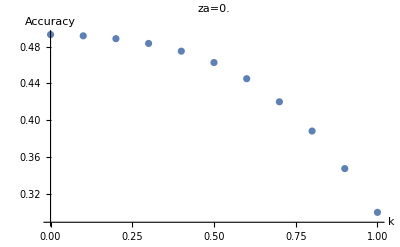

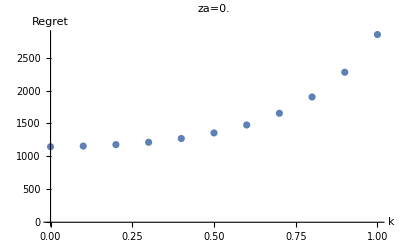

-Graphics-

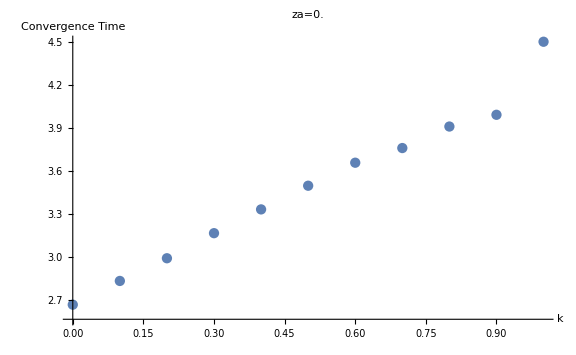

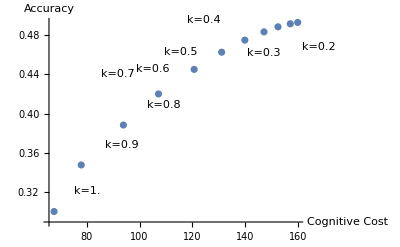

67.5292

{67.5289,3029/10100}k=1.

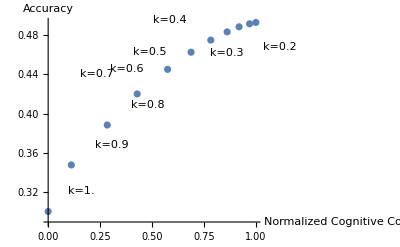

{}

Minimum distance:

0.397688

0.9

{{0.,1.},{0.1,0.970355},{0.2,0.921639},{0.3,0.867312},{0.4,0.794501},{0.5,0.709703},{0.6,0.615382},{0.7,0.506763},{0.8,0.431141},{0.9,0.397688},{1.,0.439659}}

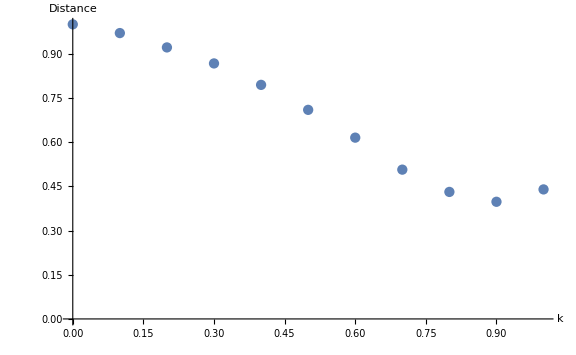

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chds"
zName = "za_0" (*as before*)
path="polimi/Magistrale/secondo_anno/thesis/notebooks/";
za=0.0;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
G=4;
n=15;
costAccuracyList={};
averagedMetrics =GetAveragedMetrics[za, path1, path2, path3]
accuracies = averagedMetrics[[1]];
regrets = averagedMetrics[[2]];
convergenceTimes = averagedMetrics[[3]];
costs={};
pointsToDisplay=List[];
kStart=0.3;
kEnd=0.5;
testTimes={};
Graphics[ListPlot[accuracies, AxesLabel->{"k","Accuracy"}, PlotLabel->"za="<>ToString[za]]]
Graphics[ListPlot[regrets, AxesLabel->{"k","Regret"}, PlotLabel->"za="<>ToString[za]]]
accuracyPlot = ListPlot[
accuracies,
PlotStyle->Blue,
ImagePadding->70,
Frame->{True,True,True,False},
FrameLabel->{Style["k",Bold,16],Style["Accuracy", Bold, 16]},
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Blue, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16]},   
PlotLabel->Style["za="<>ToString[za],Bold,16], 
ImageSize->Full
];
regretPlot =  ListPlot[regrets, 
PlotStyle->Red,
ImagePadding->70,
Axes->False, 
Frame->{False,False,False, True}, 
FrameLabel->{{"h",Style["Regret", Bold, 16]},{"h","H"}},
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Red, Thick, FontSize->16]},
FrameTicks->{{None,All},{None,None}}, 
ImageSize->Full,
TicksStyle->Large];
ImageCompose[accuracyPlot, regretPlot]
Graphics[ListPlot[convergenceTimes,  AxesLabel->{Style["k", Bold, 16],Style["Convergence Time", Bold, 16]}, PlotLabel->"za="<>ToString[za], PlotRange->Full, ImageSize->Large]]
speedAccuracyList = {};
Do[
AppendTo[speedAccuracyList,Labeled[ {convergenceTimes[[i]][[2]], accuracies[[i]][[2]]}, Text[Style["k="<>ToString[i*0.1-0.1], Bold, 16]]]]
,{i,1,Length[accuracies]}];
Graphics[ListPlot[speedAccuracyList, AxesLabel->{Style["Convergence Time", Bold, 16],Style["Accuracy", Bold, 16]}, PlotLabel->"za="<>ToString[za], ImageSize->Full]];
	Do[
	cost=n*(convergenceTimes[[k*10+1]][[2]])*(k+(1-k)*G); 
AppendTo[costs, cost];
AppendTo[costAccuracyList, Labeled[{cost, accuracies[[Floor[10*k]+1]][[2]]}, Text["k="<>ToString[k]]]], {k,0,1,0.1}];
Graphics[ListPlot[costAccuracyList, AxesLabel->{Style["Cognitive Cost", Bold, 16],Style["Accuracy", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]]
MinDistance[costAccuracyList, {0,0.5}]
(*Export["path/folder/costacc_za_0.txt",costAccuracyList];*) (*allows to condense two cost accuracy graphs later, one per za*)
maxAccuracy = N[Max[Take[Flatten[accuracies], {2,Length[accuracies]*2, 2}]]];
maxCost = Max[costs];
remapCosts[x_]:=(x-Min[costs])/(Max[costs]-Min[costs]);
normalizedCosts = Map[remapCosts, costs];
normalizedCostAccuracyList = {};
Do[
AppendTo[normalizedCostAccuracyList, Labeled[{normalizedCosts[[Floor[10*k]+1]], accuracies[[Floor[10*k]+1]][[2]]}, Text["k="<>ToString[k]]]]
,{k,0,1,0.1}];
ListPlot[normalizedCostAccuracyList, AxesLabel->{Style["Normalized Cognitive Cost", Bold, 16],Style["Accuracy", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]
Export[path<>name<>"/costacc_"<>zName<>".txt",normalizedCostAccuracyList];
alfa = maxAccuracy/maxCost;
minDist=+Infinity;
minK=1;
distances={}
Do[
d = Sqrt[(normalizedCosts[[i]])^2+(maxAccuracy-accuracies[[i,2]])];
AppendTo[distances, {N[(i-1)/10], d}];
If[d<minDist, minDist = d; minK=N[(i-1)/10]]
,{i,1,Length[costs]}]
Print["Minimum distance:"]
minDist
minK
distances
Export[path<>name<>"/distances_"<>zName<>".txt",distances]; (*allows to condense two distance graphs later, one per za*)
ListPlot[distances, 
AxesLabel->{Style["k", Bold, 16],Style["Distance", Bold, 16]},
ImageSize->Large,
PlotRange->Full]
```

### Plotting the condensed cost/accuracy and distance graphs for za=0,0.05 - direct switch

```mathematica
name="chds";
icaZa005 = Import[path<>name<>"/costacc_za_0_0_5.txt"];
caZa005 = ToExpression[StringSplit[icaZa005, "\n"]];
dZa005 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0_0_5.txt"], "\n"]];
icaZa0 = Import[path<>name<>"/costacc_za_0.txt"];
caZa0 = ToExpression[StringSplit[icaZa0, "\n"]];
dZa0 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0.txt"], "\n"]];
legend = LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;2]],AbsoluteThickness[10]]],{"za=0.05","za=0"},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
p = Rasterize[ListPlot[{caZa005, caZa0}, AxesLabel->{Style["Normalized\nCognitive Cost", Bold, 32],Style["Accuracy", Bold, 32]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large] ,  PlotLegends->Placed[legend, Top], AxesStyle->Directive[Black, 32]]]
p1 = Rasterize[ListPlot[{dZa005, dZa0}, 
AxesLabel->{Style["k", Bold, 32],Style["Distance", Bold, 32]},
ImageSize->Full,
PlotRange->Full,
 PlotLegends->Placed[legend, Top]
, AxesStyle->Directive[Black, 32]]]
```

-Graphics-

-Graphics-

### Same as before but for cross-inhibition

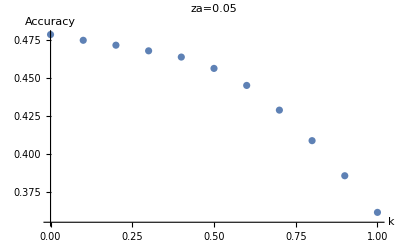

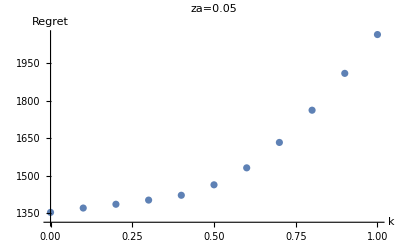

-Graphics-

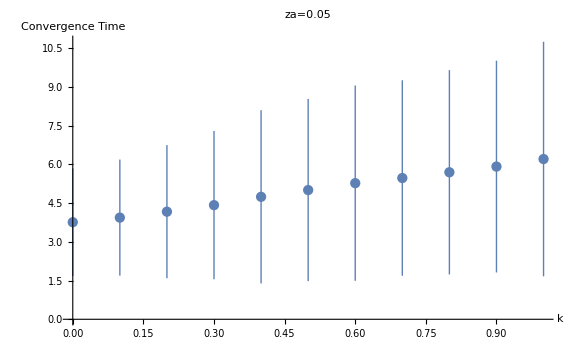

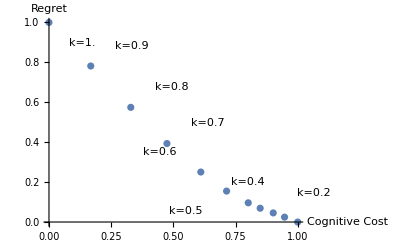

0.616158

0.7

{{0.,1.},{0.1,0.947428},{0.2,0.90278},{0.3,0.851973},{0.4,0.806924},{0.5,0.730695},{0.6,0.65993},{0.7,0.616158},{0.8,0.662018},{0.9,0.799561},{1.,1.}}

polimi/Magistrale/secondo_anno/thesis/notebooks/chci/G_4/distances_za_0_0_5.txt

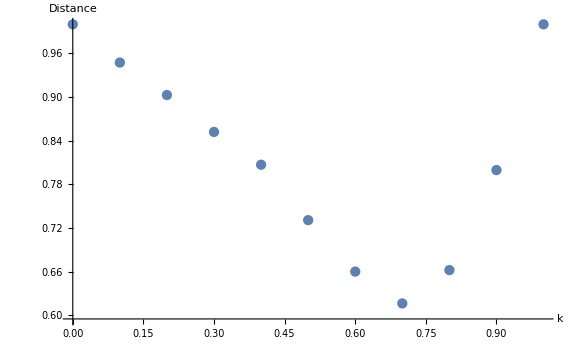

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chci/G_4";
zName = "za_0_0_5";
za=0.05;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
G=4;
n=15;
costRegretList={};
m1 = ExtractK[za, path1];
m2 = ExtractK[za, path2];
m3 = ExtractK[za, path3];
accuracies = {};
regrets = {};
convergenceTimes = {};
testTimes={};
stds={};
costs={};
pointsToDisplay=List[];
kStart=0.3;
kEnd=0.5;
theRegrets={};
Do[
a1 = m1[[1]][[k*10+1]][[2]];
a2 = m2[[1]][[k*10+1]][[2]];
a3 = m3[[1]][[k*10+1]][[2]];
a = (a1+a2+a3)/3;
r = (m1[[2]][[k*10+1]][[2]]+m2[[2]][[k*10+1]][[2]]+m3[[3]][[k*10+1]][[2]])/3;
AppendTo[theRegrets, r];
timeList1 = m1[[5]][[k*10+1]];
timeList2 = m2[[5]][[k*10+1]];
timeList3 = m3[[5]][[k*10+1]];
timeList = Join[timeList1, timeList2, timeList3];
onlyTimeList = timeList[[All,3]];
AppendTo[accuracies, {k, a}];
AppendTo[regrets, {k,r}];
AppendTo[convergenceTimes, {k,Total[onlyTimeList]/Length[onlyTimeList]}];
AppendTo[stds, {k, PlusMinus[Total[onlyTimeList]/Length[onlyTimeList], StandardDeviation[onlyTimeList]]}];
,{k,0,1,0.1}]
Graphics[ListPlot[accuracies, AxesLabel->{"k","Accuracy"}, PlotLabel->"za="<>ToString[za]]]
Graphics[ListPlot[regrets, AxesLabel->{"k","Regret"}, PlotLabel->"za="<>ToString[za]]]
accuracyPlot = ListPlot[
accuracies,
PlotStyle->Blue,
ImagePadding->100,
Frame->{True,True,True,False},
FrameLabel->{Style["k",Bold,30],Style["Accuracy", Bold, 16]},
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Blue, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16]},   
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameTicksStyle->Directive[25],
ImageSize->Full
];
regretPlot =  ListPlot[regrets, 
PlotStyle->Red,
ImagePadding->100,
Axes->False, 
Frame->{False,False,False, True}, 
FrameLabel->{{"h",Style["Regret", Bold, 16]},{"h","H"}},
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Red, Thick, FontSize->16]},
FrameTicks->{{None,All},{None,None}}, 
ImageSize->Full,
TicksStyle->Large,
FrameTicksStyle->Directive[25]];
ImageCompose[accuracyPlot, regretPlot]
Graphics[ListPlot[stds,  AxesLabel->{Style["k", Bold, 16],Style["Convergence Time", Bold, 16]}, PlotLabel->"za="<>ToString[za], PlotRange->Full, ImageSize->Large]]
(*plot the normalized regret*)
maxRegret = Max[theRegrets];
minRegret = Min[theRegrets];
remapRegret[x_]:= (x-minRegret)/(maxRegret-minRegret);
normalizedRegrets = Map[remapRegret, theRegrets];
Do[
	cost=n*(stds[[k*10+1]][[2]][[1]](*+stds[[k*10+1]][[2]][[2]]*))*(k+(1-k)*G); 
AppendTo[costs, cost];
, {k,0,1,0.1}];
remapCosts[x_]:=(x-Min[costs])/(Max[costs]-Min[costs]);
normalizedCosts = Map[remapCosts, costs];
Do[
AppendTo[costRegretList, Labeled[{normalizedCosts[[Floor[10*k]+1]], normalizedRegrets[[Floor[10*k]+1]]}, Text["k="<>ToString[k]]]]
,{k,0,1,0.1}];
Export["polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/costreg_"<>zName<>".txt",costRegretList];
Graphics[ListPlot[costRegretList, AxesLabel->{Style["Cognitive Cost", Bold, 16],Style["Regret", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]]
distances={};
minDist=+Infinity;
minK=0.0;
Do[
d = EuclideanDistance[{0,0}, costRegretList[[i]][[1]]];
AppendTo[distances, {N[(i-1)/10], d}];
If[d<minDist, minDist = d; minK=N[(i-1)/10]]
,{i,1,Length[costs]}]
minDist
minK
distances
Export["polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/distances_"<>zName<>".txt",distances]
ListPlot[distances, 
AxesLabel->{Style["k", Bold, 16],Style["Distance", Bold, 16]},
ImageSize->Large,
PlotRange->Full]
```

```mathematica
icaZa005 = Import[path<>name<>"/costreg_za_0_0_5.txt"];
caZa005 = ToExpression[StringSplit[icaZa005, "\n"]];
dZa005 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0_0_5.txt"], "\n"]];
icaZa0 = Import[path<>name<>"/costreg_za_0.txt"];
caZa0 = ToExpression[StringSplit[icaZa0, "\n"]];
dZa0 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0.txt"], "\n"]];
legend = LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;2]],AbsoluteThickness[10]]],{"za=0.05","za=0"},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
p = Rasterize[ListPlot[{caZa005, caZa0}, AxesLabel->{Style["Normalized\nCognitive Cost", Bold, 32],Style["Normalized Regret", Bold, 32]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large] ,  PlotLegends->Placed[legend, Top], AxesStyle->Directive[Black, 32]]]
p1 = Rasterize[ListPlot[{dZa005, dZa0}, 
AxesLabel->{Style["k", Bold, 32],Style["Distance", Bold, 32]},
ImageSize->Full,
PlotRange->Full,
 PlotLegends->Placed[legend, Top]
, AxesStyle->Directive[Black, 32]]]
```

```mathematica
(*m1 = ExtractK[za, path1];
m2 = ExtractK[za, path2];
m3 = ExtractK[za, path3];*)
(*accuracies = {};
regrets = {};
convergenceTimes = {};
testTimes={};
stds={};
costs={};
pointsToDisplay=List[];
kStart=0.3;
kEnd=0.5
Do[
a1 = m1[[1]][[k*10+1]][[2]];
a2 = m2[[1]][[k*10+1]][[2]];
a3 = m3[[1]][[k*10+1]][[2]];
a = (a1+a2+a3)/3;
r = (m1[[2]][[k*10+1]][[2]]+m2[[2]][[k*10+1]][[2]]+m3[[3]][[k*10+1]][[2]])/3;
timeList1 = m1[[5]][[k*10+1]];
timeList2 = m2[[5]][[k*10+1]];
timeList3 = m3[[5]][[k*10+1]];
timeList = Join[timeList1, timeList2, timeList3];
onlyTimeList = timeList[[All,3]];
AppendTo[accuracies, {k, a}];
AppendTo[regrets, {k,r}];
AppendTo[convergenceTimes, {k, Total[onlyTimeList]/Length[onlyTimeList]}];
AppendTo[stds, {k, PlusMinus[(m1[[3,k*10+1, 2]]+m2[[3,k*10+1,2]]+m3[[3,k*10+1,2]])/3,(m1[[4,k*10+1, 2,2]]+m2[[4,k*10+1,2,2]]+m3[[4,k*10+1,2,2]])/3 ]}];
,{k,0,1,0.1}]*)
```

-Graphics-

### Plotting the parameter space of a heterogeneous model, showing the change for 3 values of k

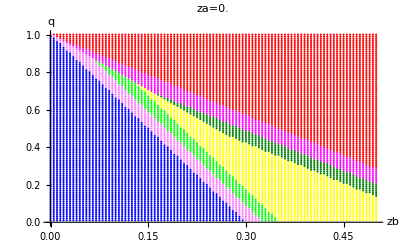

```mathematica
path =  "/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/chds/more_a/za_0/";
za=0.0;
awinspoints={};
bwinspoints={};
deadlockpoints={};
pointsToDisplay=List[];
Do[
awinspoints = ToExpression[StringSplit[Import[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]] ;
bwinspoints =ToExpression[StringSplit[ Import[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
deadlockpoints =ToExpression[StringSplit[Import[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
AppendTo[pointsToDisplay, {awinspoints, bwinspoints, deadlockpoints, k}];
, {k,0.8,1,0.1}];
awinsPointsK08 = pointsToDisplay[[1,1]];
bwinsPointsK08 = pointsToDisplay[[1,2]];
deadlockPointsK08=pointsToDisplay[[1,3]];
awinsPointsK09 = pointsToDisplay[[2,1]];
bwinsPointsK09 = pointsToDisplay[[2,2]];
deadlockPointsK09=pointsToDisplay[[2,3]];
awinsPointsK1 = pointsToDisplay[[3,1]];
bwinsPointsK1 = pointsToDisplay[[3,2]];
deadlockPointsK1=pointsToDisplay[[3,3]];
commonAPoints={};
commonBPoints={};
commonDeadlockPoints={};
firstDeadlockPointsBottom={}; (*points that are associated to the victory of A in k=0.9 but resulted in a deadlock in k=1*)
secondDeadlockPointsBottom={};(*points that are associated to the victory of A in k=0.8 but resulted in a deadlock in k=0.9*)
firstDeadlockPointsTop={};(*points that are associated to the victory of B in k=0.9 but resulted in a deadlock in k=1*)
secondDeadlockPointsTop={};(*points that are associated to the victory of B in k=0.8 but resulted in a deadlock in k=0.9*)
Do[
If[MemberQ[ awinsPointsK08,{zb,q}]&&MemberQ[awinsPointsK1,{zb,q}], AppendTo[commonAPoints, {zb,q}],
If[MemberQ[ bwinsPointsK08,{zb,q}]&&MemberQ[bwinsPointsK09,{zb,q}]&&MemberQ[ bwinsPointsK1,{zb,q}], AppendTo[commonBPoints, {zb,q}], 
If[MemberQ[ deadlockPointsK08,{zb,q}]&&MemberQ[deadlockPointsK09,{zb,q}]&&MemberQ[ deadlockPointsK1,{zb,q}], AppendTo[commonDeadlockPoints, {zb,q}],
If[MemberQ[ awinsPointsK08,{zb,q}]&&MemberQ[deadlockPointsK09,{zb,q}], AppendTo[secondDeadlockPointsBottom, {zb,q}],
If[MemberQ[ awinsPointsK09,{zb,q}]&&MemberQ[ deadlockPointsK1,{zb,q}], AppendTo[firstDeadlockPointsBottom, {zb,q}],
If[MemberQ[ bwinsPointsK08,{zb,q}]&&MemberQ[ deadlockPointsK09,{zb,q}], AppendTo[secondDeadlockPointsTop, {zb,q}],
AppendTo[firstDeadlockPointsTop, {zb,q}]
]

]
]]]]
, {zb,0,0.5,0.005}, {q,0.01(*0 for p_alfa, 0.01 for combinatorial*),1,0.01}]
ListPlot[{commonAPoints, commonBPoints, commonDeadlockPoints, secondDeadlockPointsBottom, firstDeadlockPointsBottom, secondDeadlockPointsTop, firstDeadlockPointsTop}, PlotStyle->{Blue, Red, Yellow,Green, RGBColor[1,0.5,1],RGBColor[0,0.5,0], RGBColor[1,0,1]}, PlotLabel->"za="<>ToString[za], AxesLabel->{Style["zb", Bold, FontSize->16],Style["q", Bold, FontSize->16]}, ImageSize->Full, LabelStyle->Directive[Black]]
```

```mathematica
ListPlot[{commonAPoints, commonBPoints, commonDeadlockPoints, secondDeadlockPointsBottom, firstDeadlockPointsBottom, secondDeadlockPointsTop, firstDeadlockPointsTop}, PlotStyle->{Blue, Red, Yellow,Green, RGBColor[1,0.5,1],RGBColor[0,0.5,0], RGBColor[1,0,1]}, AxesLabel->{Style["zb", Bold, 32],Style["q", Bold, 32]}, ImageSize->Full, LabelStyle->Directive[Black, Large]]
```

ListPlot::lpn: {{},{},{},{},{},{},{{0.001,0.},{0.001,0.01},{0.001,0.02},{0.001,0.03},{0.001,0.04},{0.001,0.05},{0.001,0.06},{0.001,0.07},{0.001,0.08},{0.001,0.09},«10090»}} is not a list of numbers or pairs of numbers.

### plotting the parameter space of a model

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
```

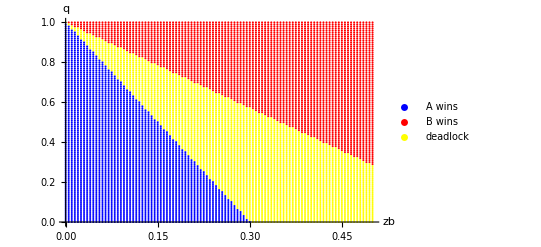

```mathematica
ParameterSpaceK[1, 0, "/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/ds_hetero_initial_points/more_a/za_0/"]
```

### Bayesian Risk

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl";
name = "chci/G_4";
zName = "za_0";
za=0.0;
n=15;
G=4;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
metrics = GetAveragedMetrics[za, path1, path2, path3,n, G ];
accuracies = metrics[[1]];
regrets = metrics[[2]]/10000
convergenceTimes = metrics[[3]];
costs = metrics[[4]];
bayesianRiskList = List[];
minimumBRList = List[];
minimumBRValuesList = List[];
Do[
minBR ={{-1,-1}, +Infinity};
Do[
br = costs[[k*10+1]]+h *(regrets[[k*10+1]][[2]]);
AppendTo[bayesianRiskList, {k, h, br}];
If[br<minBR[[2]], minBR = {{k,h}, br}]
,{k,0,1,0.1}];
AppendTo[minimumBRList, minBR[[1]]];
AppendTo[minimumBRValuesList, minBR[[2]]];
,{h,0,1000}];
pl1 = Rasterize[ListDensityPlot[bayesianRiskList, ColorFunction->"BlueGreenYellow",Axes->True, PlotLabel->Style["Bayesian Risk - "<>name<>" - za="<>ToString[N[za]], 32], FrameLabel->{Style["k", 32], Style["h", 32]}, ImageSize->Full, PlotLegends->Automatic, Epilog->ListPlot[minimumBRList, PlotStyle->{Red, PointSize->Small}, PlotRange->{{0,1},{0,1000}}][[1]]]]
minimumBRList
minimumBRValuesList
```

{{0.,0.166515},{0.00001,0.16821},{0.00002,0.169895},{0.00003,0.171505},{0.00004,0.173098},{0.00005,0.175164},{0.00006,0.17918},{0.00007,0.186045},{0.00008,0.194892},{0.00009,0.20571},{0.0001,0.217263}}

-Graphics-

{{1.,0},{1.,1},{1.,2},{1.,3},{1.,4},{1.,5},{1.,6},{1.,7},{1.,8},{1.,9},{1.,10},{1.,11},{1.,12},{1.,13},{1.,14},{1.,15},{1.,16},{1.,17},{1.,18},{1.,19},{1.,20},{1.,21},{1.,22},{1.,23},{1.,24},{1.,25},{1.,26},{1.,27},{1.,28},{1.,29},{1.,30},{1.,31},{1.,32},{1.,33},{1.,34},{1.,35},{1.,36},{1.,37},{1.,38},{1.,39},{1.,40},{1.,41},{1.,42},{1.,43},{1.,44},{1.,45},{1.,46},{1.,47},{1.,48},{1.,49},{1.,50},{1.,51},{1.,52},{1.,53},{1.,54},{1.,55},{1.,56},{1.,57},{1.,58},{1.,59},{1.,60},{1.,61},{1.,62},{1.,63},{1.,64},{1.,65},{1.,66},{1.,67},{1.,68},{1.,69},{1.,70},{1.,71},{1.,72},{1.,73},{1.,74},{1.,75},{1.,76},{1.,77},{1.,78},{1.,79},{1.,80},{1.,81},{1.,82},{1.,83},{1.,84},{1.,85},{1.,86},{1.,87},{1.,88},{1.,89},{1.,90},{1.,91},{1.,92},{1.,93},{1.,94},{1.,95},{1.,96},{1.,97},{1.,98},{1.,99},{1.,100},{1.,101},{1.,102},{1.,103},{1.,104},{1.,105},{1.,106},{1.,107},{1.,108},{1.,109},{1.,110},{1.,111},{1.,112},{1.,113},{1.,114},{1.,115},{1.,116},{1.,117},{1.,118},{1.,119},{1.,120},{1.,121},{1.,122},{1.,123},{1.,124},{1.,125},{1.,126},{1.,127},{1.,128},{1.,129},{1.,130},{1.,131},{1.,132},{1.,133},{1.,134},{1.,135},{1.,136},{1.,137},{1.,138},{1.,139},{1.,140},{1.,141},{1.,142},{1.,143},{1.,144},{1.,145},{1.,146},{1.,147},{1.,148},{1.,149},{1.,150},{1.,151},{1.,152},{1.,153},{1.,154},{1.,155},{1.,156},{1.,157},{1.,158},{1.,159},{1.,160},{1.,161},{1.,162},{1.,163},{1.,164},{1.,165},{1.,166},{1.,167},{1.,168},{1.,169},{1.,170},{1.,171},{1.,172},{1.,173},{1.,174},{1.,175},{1.,176},{1.,177},{1.,178},{1.,179},{1.,180},{1.,181},{1.,182},{1.,183},{1.,184},{1.,185},{1.,186},{1.,187},{1.,188},{1.,189},{1.,190},{1.,191},{1.,192},{1.,193},{1.,194},{1.,195},{1.,196},{1.,197},{1.,198},{1.,199},{1.,200},{1.,201},{1.,202},{1.,203},{1.,204},{1.,205},{1.,206},{1.,207},{1.,208},{1.,209},{1.,210},{1.,211},{1.,212},{1.,213},{1.,214},{1.,215},{1.,216},{1.,217},{1.,218},{1.,219},{1.,220},{1.,221},{1.,222},{1.,223},{1.,224},{1.,225},{1.,226},{1.,227},{1.,228},{1.,229},{1.,230},{1.,231},{1.,232},{1.,233},{1.,234},{1.,235},{1.,236},{1.,237},{1.,238},{1.,239},{1.,240},{1.,241},{1.,242},{1.,243},{1.,244},{1.,245},{1.,246},{1.,247},{1.,248},{1.,249},{1.,250},{1.,251},{1.,252},{1.,253},{1.,254},{1.,255},{1.,256},{1.,257},{1.,258},{1.,259},{1.,260},{1.,261},{1.,262},{1.,263},{1.,264},{1.,265},{1.,266},{1.,267},{1.,268},{1.,269},{1.,270},{1.,271},{1.,272},{1.,273},{1.,274},{1.,275},{1.,276},{1.,277},{1.,278},{1.,279},{1.,280},{1.,281},{1.,282},{1.,283},{1.,284},{1.,285},{1.,286},{1.,287},{1.,288},{1.,289},{1.,290},{1.,291},{1.,292},{1.,293},{1.,294},{1.,295},{1.,296},{1.,297},{1.,298},{1.,299},{1.,300},{1.,301},{1.,302},{1.,303},{1.,304},{1.,305},{1.,306},{1.,307},{1.,308},{1.,309},{1.,310},{1.,311},{1.,312},{1.,313},{1.,314},{1.,315},{1.,316},{1.,317},{1.,318},{1.,319},{1.,320},{1.,321},{1.,322},{1.,323},{1.,324},{1.,325},{1.,326},{1.,327},{1.,328},{1.,329},{1.,330},{1.,331},{1.,332},{1.,333},{1.,334},{1.,335},{1.,336},{1.,337},{1.,338},{1.,339},{1.,340},{1.,341},{1.,342},{1.,343},{1.,344},{1.,345},{1.,346},{1.,347},{1.,348},{1.,349},{1.,350},{1.,351},{1.,352},{1.,353},{1.,354},{1.,355},{1.,356},{1.,357},{1.,358},{1.,359},{1.,360},{1.,361},{1.,362},{1.,363},{1.,364},{1.,365},{1.,366},{1.,367},{1.,368},{1.,369},{1.,370},{1.,371},{1.,372},{1.,373},{1.,374},{1.,375},{1.,376},{1.,377},{1.,378},{1.,379},{1.,380},{1.,381},{1.,382},{1.,383},{1.,384},{1.,385},{1.,386},{1.,387},{1.,388},{1.,389},{1.,390},{1.,391},{1.,392},{1.,393},{1.,394},{1.,395},{1.,396},{1.,397},{1.,398},{1.,399},{1.,400},{1.,401},{1.,402},{1.,403},{1.,404},{1.,405},{1.,406},{1.,407},{1.,408},{1.,409},{1.,410},{1.,411},{1.,412},{1.,413},{1.,414},{1.,415},{1.,416},{1.,417},{1.,418},{1.,419},{1.,420},{1.,421},{1.,422},{1.,423},{1.,424},{1.,425},{1.,426},{1.,427},{1.,428},{1.,429},{1.,430},{1.,431},{1.,432},{1.,433},{1.,434},{1.,435},{1.,436},{1.,437},{1.,438},{1.,439},{1.,440},{1.,441},{1.,442},{1.,443},{1.,444},{1.,445},{1.,446},{1.,447},{1.,448},{1.,449},{1.,450},{1.,451},{1.,452},{1.,453},{1.,454},{1.,455},{1.,456},{1.,457},{1.,458},{1.,459},{1.,460},{1.,461},{1.,462},{1.,463},{1.,464},{1.,465},{1.,466},{1.,467},{1.,468},{1.,469},{1.,470},{1.,471},{1.,472},{1.,473},{1.,474},{1.,475},{1.,476},{1.,477},{1.,478},{1.,479},{1.,480},{1.,481},{1.,482},{1.,483},{1.,484},{1.,485},{1.,486},{1.,487},{1.,488},{1.,489},{1.,490},{1.,491},{1.,492},{1.,493},{1.,494},{1.,495},{1.,496},{1.,497},{1.,498},{1.,499},{1.,500},{1.,501},{1.,502},{1.,503},{1.,504},{1.,505},{1.,506},{1.,507},{1.,508},{1.,509},{1.,510},{1.,511},{1.,512},{1.,513},{1.,514},{1.,515},{1.,516},{1.,517},{1.,518},{1.,519},{1.,520},{1.,521},{1.,522},{1.,523},{1.,524},{1.,525},{1.,526},{1.,527},{1.,528},{1.,529},{1.,530},{1.,531},{1.,532},{1.,533},{1.,534},{1.,535},{1.,536},{1.,537},{1.,538},{1.,539},{1.,540},{1.,541},{1.,542},{1.,543},{1.,544},{1.,545},{1.,546},{1.,547},{1.,548},{1.,549},{1.,550},{1.,551},{1.,552},{1.,553},{1.,554},{1.,555},{1.,556},{1.,557},{1.,558},{1.,559},{1.,560},{1.,561},{1.,562},{1.,563},{1.,564},{1.,565},{1.,566},{1.,567},{1.,568},{1.,569},{1.,570},{1.,571},{1.,572},{1.,573},{1.,574},{1.,575},{1.,576},{1.,577},{1.,578},{1.,579},{1.,580},{1.,581},{1.,582},{1.,583},{1.,584},{1.,585},{1.,586},{1.,587},{1.,588},{1.,589},{1.,590},{1.,591},{1.,592},{1.,593},{1.,594},{1.,595},{1.,596},{1.,597},{1.,598},{1.,599},{1.,600},{1.,601},{1.,602},{1.,603},{1.,604},{1.,605},{1.,606},{1.,607},{1.,608},{1.,609},{1.,610},{1.,611},{1.,612},{1.,613},{1.,614},{1.,615},{1.,616},{1.,617},{1.,618},{1.,619},{1.,620},{1.,621},{1.,622},{1.,623},{1.,624},{1.,625},{1.,626},{1.,627},{1.,628},{1.,629},{1.,630},{1.,631},{1.,632},{1.,633},{1.,634},{1.,635},{1.,636},{1.,637},{1.,638},{1.,639},{1.,640},{1.,641},{1.,642},{1.,643},{1.,644},{1.,645},{1.,646},{1.,647},{1.,648},{1.,649},{1.,650},{1.,651},{1.,652},{1.,653},{1.,654},{1.,655},{1.,656},{1.,657},{1.,658},{1.,659},{1.,660},{1.,661},{1.,662},{1.,663},{1.,664},{1.,665},{1.,666},{1.,667},{1.,668},{1.,669},{1.,670},{1.,671},{1.,672},{1.,673},{1.,674},{1.,675},{1.,676},{1.,677},{1.,678},{1.,679},{1.,680},{1.,681},{1.,682},{1.,683},{1.,684},{1.,685},{1.,686},{1.,687},{1.,688},{1.,689},{1.,690},{1.,691},{1.,692},{1.,693},{1.,694},{1.,695},{1.,696},{1.,697},{1.,698},{1.,699},{1.,700},{1.,701},{1.,702},{1.,703},{1.,704},{1.,705},{1.,706},{1.,707},{1.,708},{1.,709},{1.,710},{1.,711},{1.,712},{1.,713},{1.,714},{1.,715},{1.,716},{1.,717},{1.,718},{1.,719},{1.,720},{1.,721},{1.,722},{1.,723},{1.,724},{1.,725},{1.,726},{1.,727},{1.,728},{1.,729},{1.,730},{1.,731},{1.,732},{1.,733},{1.,734},{1.,735},{1.,736},{1.,737},{1.,738},{1.,739},{1.,740},{1.,741},{1.,742},{1.,743},{1.,744},{1.,745},{1.,746},{1.,747},{1.,748},{1.,749},{1.,750},{1.,751},{1.,752},{1.,753},{1.,754},{1.,755},{1.,756},{1.,757},{1.,758},{1.,759},{1.,760},{1.,761},{1.,762},{1.,763},{1.,764},{1.,765},{1.,766},{1.,767},{1.,768},{1.,769},{1.,770},{1.,771},{1.,772},{1.,773},{1.,774},{1.,775},{1.,776},{1.,777},{1.,778},{1.,779},{1.,780},{1.,781},{1.,782},{1.,783},{1.,784},{1.,785},{1.,786},{1.,787},{1.,788},{1.,789},{1.,790},{1.,791},{1.,792},{1.,793},{1.,794},{1.,795},{1.,796},{1.,797},{1.,798},{1.,799},{1.,800},{1.,801},{1.,802},{1.,803},{1.,804},{1.,805},{1.,806},{1.,807},{1.,808},{1.,809},{1.,810},{1.,811},{1.,812},{1.,813},{1.,814},{1.,815},{1.,816},{1.,817},{1.,818},{1.,819},{1.,820},{1.,821},{1.,822},{1.,823},{1.,824},{1.,825},{1.,826},{1.,827},{1.,828},{1.,829},{1.,830},{1.,831},{1.,832},{1.,833},{1.,834},{1.,835},{1.,836},{1.,837},{1.,838},{1.,839},{1.,840},{1.,841},{1.,842},{1.,843},{1.,844},{1.,845},{1.,846},{1.,847},{1.,848},{1.,849},{1.,850},{1.,851},{1.,852},{1.,853},{1.,854},{1.,855},{1.,856},{1.,857},{1.,858},{1.,859},{1.,860},{1.,861},{1.,862},{1.,863},{1.,864},{1.,865},{1.,866},{1.,867},{1.,868},{1.,869},{1.,870},{1.,871},{1.,872},{1.,873},{1.,874},{1.,875},{1.,876},{1.,877},{1.,878},{1.,879},{1.,880},{1.,881},{1.,882},{1.,883},{1.,884},{1.,885},{1.,886},{1.,887},{1.,888},{1.,889},{1.,890},{1.,891},{1.,892},{1.,893},{1.,894},{1.,895},{1.,896},{1.,897},{1.,898},{1.,899},{1.,900},{1.,901},{1.,902},{1.,903},{1.,904},{1.,905},{1.,906},{1.,907},{1.,908},{1.,909},{1.,910},{1.,911},{1.,912},{1.,913},{1.,914},{1.,915},{1.,916},{1.,917},{1.,918},{1.,919},{1.,920},{1.,921},{1.,922},{1.,923},{1.,924},{1.,925},{1.,926},{1.,927},{1.,928},{1.,929},{1.,930},{1.,931},{1.,932},{1.,933},{1.,934},{1.,935},{1.,936},{1.,937},{1.,938},{1.,939},{1.,940},{1.,941},{1.,942},{1.,943},{1.,944},{1.,945},{1.,946},{1.,947},{1.,948},{1.,949},{1.,950},{1.,951},{1.,952},{1.,953},{1.,954},{1.,955},{1.,956},{1.,957},{1.,958},{1.,959},{1.,960},{1.,961},{1.,962},{1.,963},{1.,964},{1.,965},{1.,966},{1.,967},{1.,968},{1.,969},{1.,970},{1.,971},{1.,972},{1.,973},{1.,974},{1.,975},{1.,976},{1.,977},{1.,978},{1.,979},{1.,980},{1.,981},{1.,982},{1.,983},{1.,984},{1.,985},{1.,986},{1.,987},{1.,988},{1.,989},{1.,990},{1.,991},{1.,992},{1.,993},{1.,994},{1.,995},{1.,996},{1.,997},{1.,998},{1.,999},{1.,1000}}

{91.0222,91.2395,91.4567,91.674,91.8913,92.1085,92.3258,92.543,92.7603,92.9776,93.1948,93.4121,93.6294,93.8466,94.0639,94.2811,94.4984,94.7157,94.9329,95.1502,95.3675,95.5847,95.802,96.0192,96.2365,96.4538,96.671,96.8883,97.1056,97.3228,97.5401,97.7573,97.9746,98.1919,98.4091,98.6264,98.8437,99.0609,99.2782,99.4954,99.7127,99.93,100.147,100.364,100.582,100.799,101.016,101.234,101.451,101.668,101.885,102.103,102.32,102.537,102.754,102.972,103.189,103.406,103.623,103.841,104.058,104.275,104.492,104.71,104.927,105.144,105.362,105.579,105.796,106.013,106.231,106.448,106.665,106.882,107.1,107.317,107.534,107.751,107.969,108.186,108.403,108.62,108.838,109.055,109.272,109.49,109.707,109.924,110.141,110.359,110.576,110.793,111.01,111.228,111.445,111.662,111.879,112.097,112.314,112.531,112.748,112.966,113.183,113.4,113.618,113.835,114.052,114.269,114.487,114.704,114.921,115.138,115.356,115.573,115.79,116.007,116.225,116.442,116.659,116.876,117.094,117.311,117.528,117.746,117.963,118.18,118.397,118.615,118.832,119.049,119.266,119.484,119.701,119.918,120.135,120.353,120.57,120.787,121.004,121.222,121.439,121.656,121.874,122.091,122.308,122.525,122.743,122.96,123.177,123.394,123.612,123.829,124.046,124.263,124.481,124.698,124.915,125.132,125.35,125.567,125.784,126.001,126.219,126.436,126.653,126.871,127.088,127.305,127.522,127.74,127.957,128.174,128.391,128.609,128.826,129.043,129.26,129.478,129.695,129.912,130.129,130.347,130.564,130.781,130.999,131.216,131.433,131.65,131.868,132.085,132.302,132.519,132.737,132.954,133.171,133.388,133.606,133.823,134.04,134.257,134.475,134.692,134.909,135.127,135.344,135.561,135.778,135.996,136.213,136.43,136.647,136.865,137.082,137.299,137.516,137.734,137.951,138.168,138.385,138.603,138.82,139.037,139.255,139.472,139.689,139.906,140.124,140.341,140.558,140.775,140.993,141.21,141.427,141.644,141.862,142.079,142.296,142.513,142.731,142.948,143.165,143.383,143.6,143.817,144.034,144.252,144.469,144.686,144.903,145.121,145.338,145.555,145.772,145.99,146.207,146.424,146.641,146.859,147.076,147.293,147.511,147.728,147.945,148.162,148.38,148.597,148.814,149.031,149.249,149.466,149.683,149.9,150.118,150.335,150.552,150.769,150.987,151.204,151.421,151.638,151.856,152.073,152.29,152.508,152.725,152.942,153.159,153.377,153.594,153.811,154.028,154.246,154.463,154.68,154.897,155.115,155.332,155.549,155.766,155.984,156.201,156.418,156.636,156.853,157.07,157.287,157.505,157.722,157.939,158.156,158.374,158.591,158.808,159.025,159.243,159.46,159.677,159.894,160.112,160.329,160.546,160.764,160.981,161.198,161.415,161.633,161.85,162.067,162.284,162.502,162.719,162.936,163.153,163.371,163.588,163.805,164.022,164.24,164.457,164.674,164.892,165.109,165.326,165.543,165.761,165.978,166.195,166.412,166.63,166.847,167.064,167.281,167.499,167.716,167.933,168.15,168.368,168.585,168.802,169.02,169.237,169.454,169.671,169.889,170.106,170.323,170.54,170.758,170.975,171.192,171.409,171.627,171.844,172.061,172.278,172.496,172.713,172.93,173.148,173.365,173.582,173.799,174.017,174.234,174.451,174.668,174.886,175.103,175.32,175.537,175.755,175.972,176.189,176.406,176.624,176.841,177.058,177.275,177.493,177.71,177.927,178.145,178.362,178.579,178.796,179.014,179.231,179.448,179.665,179.883,180.1,180.317,180.534,180.752,180.969,181.186,181.403,181.621,181.838,182.055,182.273,182.49,182.707,182.924,183.142,183.359,183.576,183.793,184.011,184.228,184.445,184.662,184.88,185.097,185.314,185.531,185.749,185.966,186.183,186.401,186.618,186.835,187.052,187.27,187.487,187.704,187.921,188.139,188.356,188.573,188.79,189.008,189.225,189.442,189.659,189.877,190.094,190.311,190.529,190.746,190.963,191.18,191.398,191.615,191.832,192.049,192.267,192.484,192.701,192.918,193.136,193.353,193.57,193.787,194.005,194.222,194.439,194.657,194.874,195.091,195.308,195.526,195.743,195.96,196.177,196.395,196.612,196.829,197.046,197.264,197.481,197.698,197.915,198.133,198.35,198.567,198.785,199.002,199.219,199.436,199.654,199.871,200.088,200.305,200.523,200.74,200.957,201.174,201.392,201.609,201.826,202.043,202.261,202.478,202.695,202.912,203.13,203.347,203.564,203.782,203.999,204.216,204.433,204.651,204.868,205.085,205.302,205.52,205.737,205.954,206.171,206.389,206.606,206.823,207.04,207.258,207.475,207.692,207.91,208.127,208.344,208.561,208.779,208.996,209.213,209.43,209.648,209.865,210.082,210.299,210.517,210.734,210.951,211.168,211.386,211.603,211.82,212.038,212.255,212.472,212.689,212.907,213.124,213.341,213.558,213.776,213.993,214.21,214.427,214.645,214.862,215.079,215.296,215.514,215.731,215.948,216.166,216.383,216.6,216.817,217.035,217.252,217.469,217.686,217.904,218.121,218.338,218.555,218.773,218.99,219.207,219.424,219.642,219.859,220.076,220.294,220.511,220.728,220.945,221.163,221.38,221.597,221.814,222.032,222.249,222.466,222.683,222.901,223.118,223.335,223.552,223.77,223.987,224.204,224.422,224.639,224.856,225.073,225.291,225.508,225.725,225.942,226.16,226.377,226.594,226.811,227.029,227.246,227.463,227.68,227.898,228.115,228.332,228.549,228.767,228.984,229.201,229.419,229.636,229.853,230.07,230.288,230.505,230.722,230.939,231.157,231.374,231.591,231.808,232.026,232.243,232.46,232.677,232.895,233.112,233.329,233.547,233.764,233.981,234.198,234.416,234.633,234.85,235.067,235.285,235.502,235.719,235.936,236.154,236.371,236.588,236.805,237.023,237.24,237.457,237.675,237.892,238.109,238.326,238.544,238.761,238.978,239.195,239.413,239.63,239.847,240.064,240.282,240.499,240.716,240.933,241.151,241.368,241.585,241.803,242.02,242.237,242.454,242.672,242.889,243.106,243.323,243.541,243.758,243.975,244.192,244.41,244.627,244.844,245.061,245.279,245.496,245.713,245.931,246.148,246.365,246.582,246.8,247.017,247.234,247.451,247.669,247.886,248.103,248.32,248.538,248.755,248.972,249.189,249.407,249.624,249.841,250.059,250.276,250.493,250.71,250.928,251.145,251.362,251.579,251.797,252.014,252.231,252.448,252.666,252.883,253.1,253.317,253.535,253.752,253.969,254.186,254.404,254.621,254.838,255.056,255.273,255.49,255.707,255.925,256.142,256.359,256.576,256.794,257.011,257.228,257.445,257.663,257.88,258.097,258.314,258.532,258.749,258.966,259.184,259.401,259.618,259.835,260.053,260.27,260.487,260.704,260.922,261.139,261.356,261.573,261.791,262.008,262.225,262.442,262.66,262.877,263.094,263.312,263.529,263.746,263.963,264.181,264.398,264.615,264.832,265.05,265.267,265.484,265.701,265.919,266.136,266.353,266.57,266.788,267.005,267.222,267.44,267.657,267.874,268.091,268.309,268.526,268.743,268.96,269.178,269.395,269.612,269.829,270.047,270.264,270.481,270.698,270.916,271.133,271.35,271.568,271.785,272.002,272.219,272.437,272.654,272.871,273.088,273.306,273.523,273.74,273.957,274.175,274.392,274.609,274.826,275.044,275.261,275.478,275.696,275.913,276.13,276.347,276.565,276.782,276.999,277.216,277.434,277.651,277.868,278.085,278.303,278.52,278.737,278.954,279.172,279.389,279.606,279.823,280.041,280.258,280.475,280.693,280.91,281.127,281.344,281.562,281.779,281.996,282.213,282.431,282.648,282.865,283.082,283.3,283.517,283.734,283.951,284.169,284.386,284.603,284.821,285.038,285.255,285.472,285.69,285.907,286.124,286.341,286.559,286.776,286.993,287.21,287.428,287.645,287.862,288.079,288.297,288.514,288.731,288.949,289.166,289.383,289.6,289.818,290.035,290.252,290.469,290.687,290.904,291.121,291.338,291.556,291.773,291.99,292.207,292.425,292.642,292.859,293.077,293.294,293.511,293.728,293.946,294.163,294.38,294.597,294.815,295.032,295.249,295.466,295.684,295.901,296.118,296.335,296.553,296.77,296.987,297.205,297.422,297.639,297.856,298.074,298.291,298.508,298.725,298.943,299.16,299.377,299.594,299.812,300.029,300.246,300.463,300.681,300.898,301.115,301.333,301.55,301.767,301.984,302.202,302.419,302.636,302.853,303.071,303.288,303.505,303.722,303.94,304.157,304.374,304.591,304.809,305.026,305.243,305.46,305.678,305.895,306.112,306.33,306.547,306.764,306.981,307.199,307.416,307.633,307.85,308.068,308.285}

```mathematica
minBR = {0,0,+Infinity};
Do[
If[bayesianRiskList[[i]][[3]]<minBR[[3]], minBR=bayesianRiskList[[i]]]
,{i,1, Length[bayesianRiskList]}]
minBR
maxWeightsList = List[]; (*1 per k*)
minimumBRPerKList = List[];
Do[
maxWeight = -1;
minimumBRPerK = +Infinity;
Do[
target = bayesianRiskList[[(i+1)*(j+1)]];
Print[ToString[N[target]]];
If[target[[3]]==minBR[[3]] && target[[2]]>maxWeight, maxWeight=target[[2]]];
If[target[[3]]<minimumBRPerK, minimmBRPerK = target[[3]]];
,{j, 0, 1000, 100}];
AppendTo[maxWeightsList, maxWeight];
AppendTo[minimumBRPerKList, minimumBRPerK]
,{i, 0, 10(*11 k values*)}]
maxWeightsList
minimumBRPerKList
```

{1.,0,67.5289}

{0., 0., 159.977}

{0., 91., 206.096}

{0., 182., 252.215}

{0., 273., 298.333}

{0., 364., 344.452}

{0., 455., 390.571}

{0., 546., 436.689}

{0., 637., 482.808}

{0., 728., 528.927}

{0., 819., 575.045}

{0.1, 0., 157.171}

{0.1, 91., 203.415}

{0.1, 182., 249.66}

{0.1, 273., 295.905}

{0.1, 364., 342.15}

{0.1, 455., 388.395}

{0.1, 546., 434.639}

{0.1, 637., 480.884}

{0.1, 728., 527.129}

{0.1, 819., 573.374}

{0.2, 0., 152.507}

{0.2, 91., 199.035}

{0.2, 182., 245.562}

{0.2, 273., 292.089}

{0.2, 364., 338.616}

{0.2, 455., 385.143}

{0.2, 546., 431.67}

{0.2, 637., 478.197}

{0.2, 728., 524.725}

{0.2, 819., 571.252}

{0.3, 0., 147.193}

{0.3, 91., 194.192}

{0.3, 182., 241.191}

{0.3, 273., 288.189}

{0.3, 364., 335.188}

{0.3, 455., 382.187}

{0.3, 546., 429.185}

{0.3, 637., 476.184}

{0.3, 728., 523.183}

{0.3, 819., 570.181}

{0.4, 0., 139.921}

{0.4, 91., 187.683}

{0.4, 182., 235.444}

{0.4, 273., 283.206}

{0.4, 364., 330.967}

{0.4, 455., 378.729}

{0.4, 546., 426.49}

{0.4, 637., 474.252}

{0.4, 728., 522.013}

{0.4, 819., 569.775}

{0.5, 0., 131.127}

{0.5, 91., 180.015}

{0.5, 182., 228.902}

{0.5, 273., 277.79}

{0.5, 364., 326.678}

{0.5, 455., 375.566}

{0.5, 546., 424.453}

{0.5, 637., 473.341}

{0.5, 728., 522.229}

{0.5, 819., 571.116}

{0.6, 0., 120.693}

{0.6, 91., 171.179}

{0.6, 182., 221.664}

{0.6, 273., 272.15}

{0.6, 364., 322.635}

{0.6, 455., 373.121}

{0.6, 546., 423.606}

{0.6, 637., 474.092}

{0.6, 728., 524.577}

{0.6, 819., 575.063}

{0.7, 0., 107.153}

{0.7, 91., 159.924}

{0.7, 182., 212.695}

{0.7, 273., 265.466}

{0.7, 364., 318.237}

{0.7, 455., 371.008}

{0.7, 546., 423.779}

{0.7, 637., 476.55}

{0.7, 728., 529.321}

{0.7, 819., 582.092}

{0.8, 0., 93.8399}

{0.8, 91., 149.503}

{0.8, 182., 205.166}

{0.8, 273., 260.829}

{0.8, 364., 316.493}

{0.8, 455., 372.156}

{0.8, 546., 427.819}

{0.8, 637., 483.482}

{0.8, 728., 539.145}

{0.8, 819., 594.808}

{0.9, 0., 77.8426}

{0.9, 91., 137.221}

{0.9, 182., 196.599}

{0.9, 273., 255.977}

{0.9, 364., 315.356}

{0.9, 455., 374.734}

{0.9, 546., 434.112}

{0.9, 637., 493.49}

{0.9, 728., 552.869}

{0.9, 819., 612.247}

{1., 0., 67.5289}

{1., 91., 131.238}

{1., 182., 194.947}

{1., 273., 258.656}

{1., 364., 322.365}

{1., 455., 386.074}

{1., 546., 449.783}

{1., 637., 513.492}

{1., 728., 577.201}

{1., 819., 640.91}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0}

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
bayesianRiskList[[1003]]
```

{0.1,91,203.415}

{0.,0,159.977}